```mathematica
inf1[0.1,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
Abs[-8.32212183468342221830978`10.*^62 ⅈ]
```

8.322121835×10^62

```mathematica
ing1[0,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
inf1[0,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
inf1[0.01,-1]
```

0.8052834047 ⅈ

```mathematica
inf1[0.00001,-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-8.322789738×10^62 ⅈ

```mathematica
inf1[-0.0001,-1]
```

-0.0100036916 ⅈ

```mathematica
NIntegrate[nf1[0,-1],{k3,0,200000000},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

-9199.333179 ⅈ

```mathematica
NIntegrate[nf1[0,-1],{k3,1000,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-8.322099572×10^62 ⅈ

```mathematica
nf1[0,-1]
```

-(((0.+1.82662×10^-10 ⅈ) k3 (-0.000224504-0.00270898 k3^2-0.00556632 k3^4-0.00719884 k3^6-0.00697626 k3^8-0.0024626 k3^10+0.000400772 k3^12+0.977103 k3 (0.000103037-0.00298157 k3^2-0.00298416 k3^4-0.00534397 k3^6-0.00447612 k3^8+0.00095108 k3^10) Cos[θ]+k3^2 (0.00113898+0.000462471 k3^2+0.00228749 k3^4-0.0000975371 k3^6+0.00151602 k3^8) Cos[θ]^2+0.977103 k3^3 (-0.0000785002-0.00439128 k3^2-0.00390176 k3^4+0.0000110717 k3^6) Cos[θ]^3+k3^4 (-0.00228827-0.00705769 k3^2-0.00285348 k3^4) Cos[θ]^4+0.977103 k3^5 (-0.00159034-0.00209185 k3^2) Cos[θ]^5-0.000165721 k3^6 Cos[θ]^6))/((0.998219+1. k3^2+0.977103 k3 Cos[θ])^2 (1.48868+1. k3^2+0.977103 k3 Cos[θ])^4))

```mathematica
Simplify[%32]
```

-(((0.+7.3206×10^-14 ⅈ) k3 (-0.560179-6.75941 k3^2-13.889 k3^4-17.9624 k3^6-17.407 k3^8-6.14464 k3^10+1. k3^12+(0.25121 k3-7.26922 k3^3-7.27553 k3^5-13.0289 k3^7-10.913 k3^9+2.31878 k3^11) Cos[θ]+k3^2 (2.84198+1.15395 k3^2+5.7077 k3^4-0.243373 k3^6+3.78276 k3^8) Cos[θ]^2+(-0.191388 k3^3-10.7062 k3^5-9.51269 k3^7+0.0269934 k3^9) Cos[θ]^3+(-5.70966 k3^4-17.6102 k3^6-7.11996 k3^8) Cos[θ]^4+(-3.87733 k3^5-5.10004 k3^7) Cos[θ]^5-0.413505 k3^6 Cos[θ]^6))/((0.998219+1. k3^2+0.977103 k3 Cos[θ])^2 (1.48868+1. k3^2+0.977103 k3 Cos[θ])^4))

```mathematica
inf2[-1]
```

0.+5.2702 ⅈ

```mathematica
inf2[-0.9]
```

0.+5.2702 ⅈ

```mathematica
nf2[-1]
```

((0.+6.0323 ⅈ) k3 ((-1.+0. ⅈ) ((-1.+0. ⅈ)+(1.+0. ⅈ) x)^3+(0.0356251+0. ⅈ) ((-1.+0. ⅈ)+(1.+0. ⅈ) x)^3))/(1.+k3^2-0.980928 x)^4

```mathematica
f22=f2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
ft2=f22/.{Q^2->(-t)};
```

```mathematica
nf2[t_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1}];
```

```mathematica
nf2[-1]
```

-((0.+6.28319 ⅈ) k3 (-0.0190716+L1^2)^4 (-1.+x)^3)/((k3^2+L1^2+0.0190716 x-1. L1^2 x)^4)

```mathematica
Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,Λ->1}]
```

-((0.+5.8174 ⅈ) k3 (-1.+x)^3)/((1.+k3^2-0.980928 x)^4)

```mathematica
ing2[-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
ing1[0.001,-1]
```

0.3445505747 ⅈ

```mathematica
ng2[-1]
```

0.+0. ⅈ

```mathematica
ing1[0.001,-1]
```

0.3445578113 ⅈ

```mathematica
ing1[0.1,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
ing1[-0.1,-1]
```

-787.9114263 ⅈ

```mathematica
ing1[0,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
inf1[0.1,-1]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
inf1[-0.1,-1]
```

-223.401571 ⅈ

```mathematica
inf1[-0.05,-1]
```

-15.6951019 ⅈ

```mathematica
sf1=Interpolation[Flatten[lf1,1]];
```

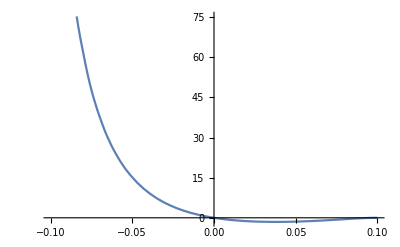

```mathematica
Plot[I*sf1[y,-1],{y,-0.1,0.1}]
```

```mathematica
sf2=Interpolation[Flatten[lf2,1]];
sf3=Interpolation[Flatten[lf3,1]];
sf4=Interpolation[Flatten[lf4,1]];
```

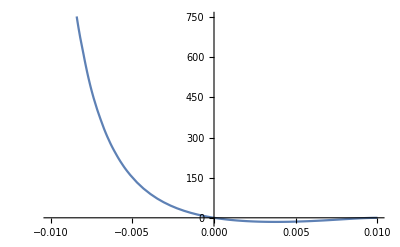

```mathematica
Plot[I*sf2[y,-1],{y,-0.01,0.01}]
```

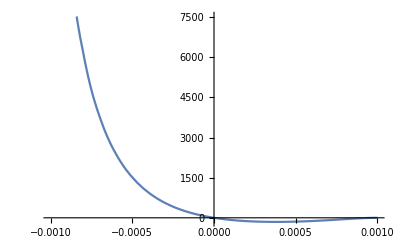

```mathematica
Plot[I*sf3[y,-1],{y,-0.001,0.001}]
```

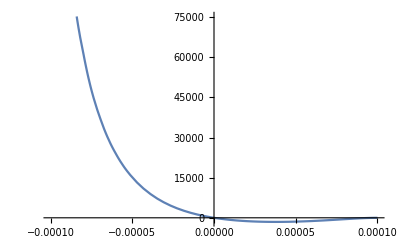

```mathematica
Plot[I*sf4[y,-1],{y,-0.0001,0.0001}]
```

```mathematica
sf4[0.00001,-1]
```

0.+776.597 ⅈ

```mathematica
sg1=Interpolation[Flatten[lg1,1]];
```

```mathematica
sg2=Interpolation[Flatten[lg2,1]];
sg3=Interpolation[Flatten[lg3,1]];
sg4=Interpolation[Flatten[lg4,1]];
```

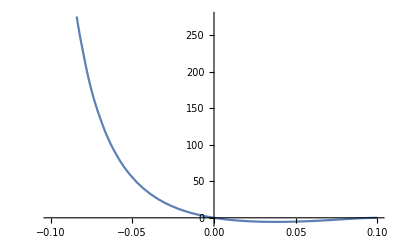

```mathematica
Plot[I*sg1[y,-1],{y,-0.1,0.1}]
```

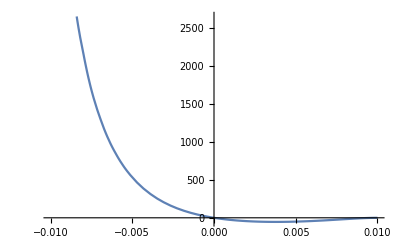

```mathematica
Plot[I*sg2[y,-1],{y,-0.01,0.01}]
```

```mathematica
sg2[0.005,-1]
```

0.+50.4064 ⅈ

```mathematica
sg2[-0.005,-1]
```

0.-534.016 ⅈ

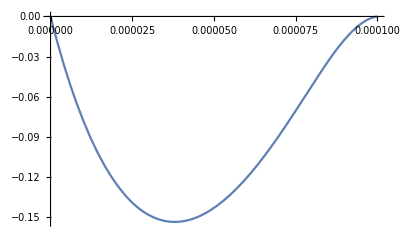

```mathematica
Plot[I*0.0001*sf4[y,-1],{y,0,0.0001}]
```

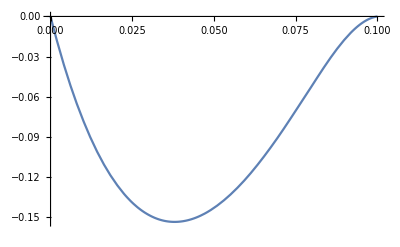

```mathematica
Plot[I*0.1*sf1[y,-1],{y,0,0.1}]
```

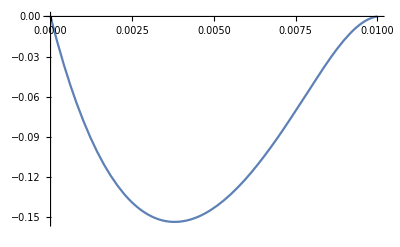

```mathematica
Plot[I*0.01*sf2[y,-1],{y,0,0.01}]
```

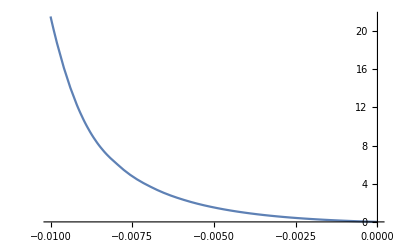

```mathematica
Plot[I*0.01*sf2[y,-1],{y,-0.01,0}]
```

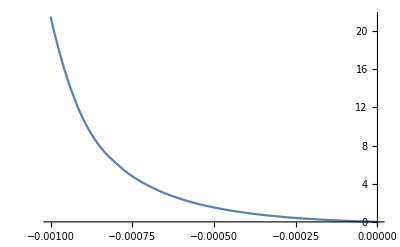

```mathematica
Plot[I*0.001*sf3[y,-1],{y,-0.001,0}]
```

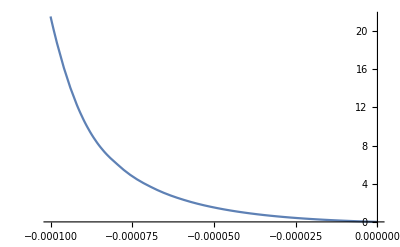

```mathematica
Plot[I*0.0001*sf4[y,-1],{y,-0.0001,0}]
```

```mathematica
Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,Λ->L1}]
```

-((0.+5.8174 ⅈ) k3 (-1.+x)^3)/((1.+k3^2-0.980928 x)^4)

```mathematica
ing1t[y_,t_]:=NIntegrate[ng1[y,t],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
lgt=ParallelTable[{{y,t},ing1t[y,t]},{y,-0.1,0.1,0.01},{t,Join[Range[-1,-0.1,0.05],Range[-0.05,-0.03562509090909091,0.005]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sgt=Interpolation[Flatten[lgt,1]];
```

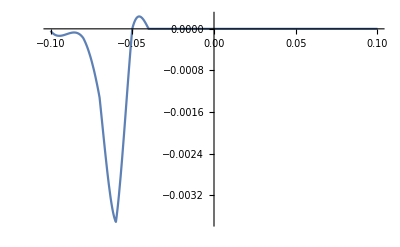

```mathematica
Plot[I*sgt[y,-1],{y,-0.1,0.1},PlotRange->All]
```

```mathematica
NIntegrate[ng1[y,-1],{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.53070254089426011104420060536540449597029648821976383117316×10^-9 ⅈ and 8.77375455509202318448056470059774737610682128482971258135138×10^-8 for the integral and error estimates.

-1.530702541×10^-9 ⅈ

```mathematica
NIntegrate[(1/y)*ng1[y,-1],{y,-0.1,0.1},{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.00259472327 ⅈ